```mathematica
Manipulate[ContourPlot[{rS*x(1-x/y)==0,rE*y(1-y)-beta/x==0},{x,-3,10},{y,-1,3},PlotLegends->Automatic],{rE,1,10},{rS,0.1,10},{beta,0.001,0.1}]
```

```mathematica
Manipulate[Plot[{-x^3+x^2-beta,0.1},{x,-0.5,2}],{beta,-0.5,1}]
```

```mathematica
Manipulate[Plot[{beta/(x*(1-x)),x},{x,-1,3}],{beta,0.001,0.3}]
```

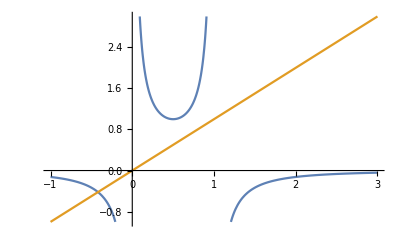

```mathematica
plt1 = Plot[{0.25/(x*(1-x)),x},{x,-1,3},PlotRange->{-1,3}]
```

```mathematica
pts1 = Table[{x,x},{x,-1.1,3.1,0.5}]
```

{{-1.1,-1.1},{-0.6,-0.6},{-0.1,-0.1},{0.4,0.4},{0.9,0.9},{1.4,1.4},{1.9,1.9},{2.4,2.4},{2.9,2.9}}

```mathematica
pts2 = Table[{0,x},{x,-1.1,3.1,0.5}];
```

```mathematica
pts3 = Table[{x,0.25/(x*(1-x))},{x,-1.1,3.1,0.5}];
```

```mathematica
allDispPts = Join[pts1,pts2,pts3]
```

{{-1.1,-1.1},{-0.6,-0.6},{-0.1,-0.1},{0.4,0.4},{0.9,0.9},{1.4,1.4},{1.9,1.9},{2.4,2.4},{2.9,2.9},{0,-1.1},{0,-0.6},{0,-0.1},{0,0.4},{0,0.9},{0,1.4},{0,1.9},{0,2.4},{0,2.9},{-1.1,-0.108225},{-0.6,-0.260417},{-0.1,-2.27273},{0.4,1.04167},{0.9,2.77778},{1.4,-0.446429},{1.9,-0.146199},{2.4,-0.0744048},{2.9,-0.0453721}}

```mathematica
uPrime[x_,y_]:=y(1-y/x);vPrime[x_,y_]:=x(1-x)-0.25/y;
```

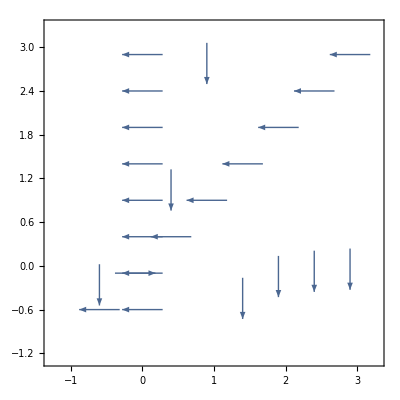

```mathematica
plt2 = VectorPlot[{vPrime[x,y]/Sqrt[uPrime[x,y]^2+vPrime[x,y]^2],uPrime[x,y]/Sqrt[uPrime[x,y]^2+vPrime[x,y]^2]},{x,-1,3},{y,-1,3},VectorPoints->allDispPts,VectorScale->{Large,1}] (*Vector Plot for Nullclines. Vectors are normalized for display*)
```

```mathematica
(*Shows the final nullcline figure*)
```

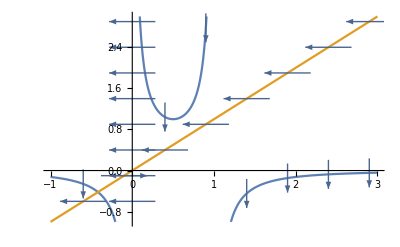

```mathematica
Show[plt1,plt2]
```

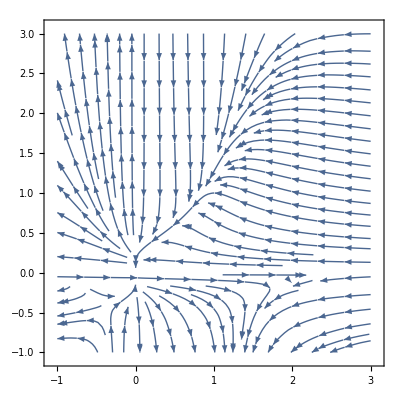

```mathematica
plt2 = StreamPlot[{x(1-x)-0.25/y,y(1-y/x)},{x,-1,3},{y,-1,3}]
```

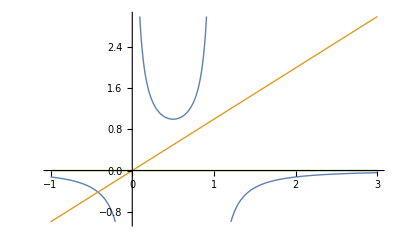

```mathematica
pltAA1 = Plot[{0.25/(x*(1-x)),x,0},{x,-1,3},PlotRange->{-1,3},PlotStyle->Thick]
```

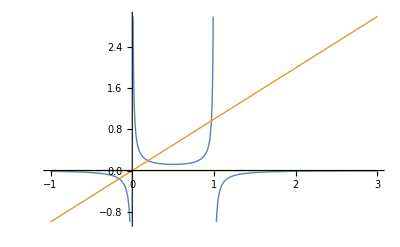

```mathematica
pltAA2 = Plot[{0.03/(x*(1-x)),x,0},{x,-1,3},PlotRange->{-1,3},PlotStyle->Thick]
```

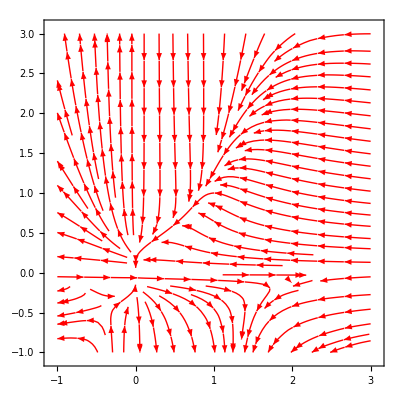

```mathematica
pltA1 = StreamPlot[{x(1-x)-0.25/y,y(1-y/x)},{x,-1,3},{y,-1,3},StreamStyle->Red]
```

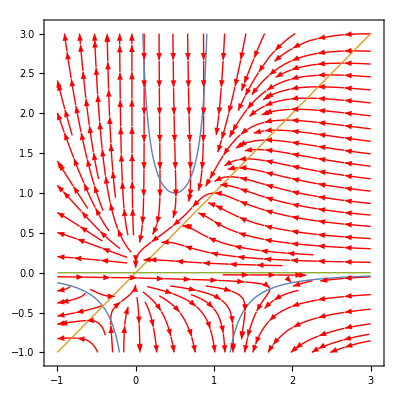

```mathematica
Show[pltA1,pltAA1] (*Density plot large values of beta*)
```

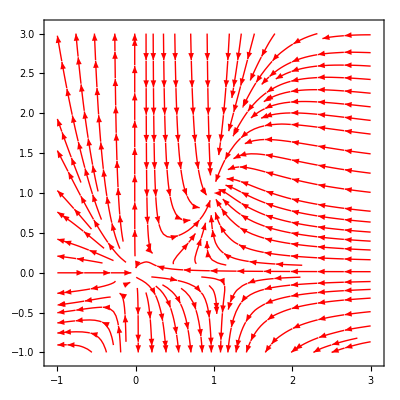

```mathematica
pltA2 = StreamPlot[{x(1-x)-0.03/y,y(1-y/x)},{x,-1,3},{y,-1,3},StreamStyle->Red]
```

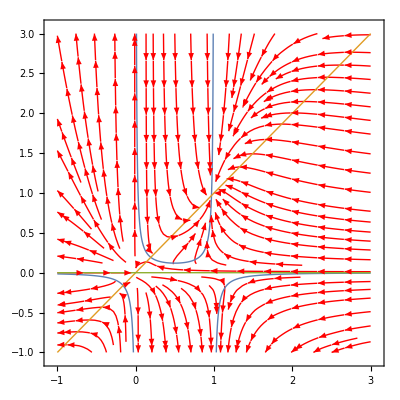

```mathematica
Show[pltA2,pltAA2] (*Density plot small value of beta*)
```